```mathematica
compareQibla=Module[{city=ToString/@{##}~Take~2,
qiblas=({{Qibla, City, Country}, {"Petra", "Wadi Musa", "Jordan"}, {"Kaāba", "Mecca", "SaudiArabia"}, {"al-Aqsa", "Jerusalem", "Israel"}}),
direction=GeoDirection@@Map[#~CityData~"Coordinates"&,{##}]&,
a=Arrow@AnglePath[{π/2-#}]&,
c=Riffle[{Red,Green,Blue,Gray},#]&,
p=If[ListQ[#],#,Rest@First@#]&,q},
q=Map[c,#/@p[qiblas]&/@{a@direction[city,Rest@#]&,First}];
p=If[Length@{##}>2,#~Append~#2&,#&];
c=MapThread[p,{q,{a@Last[{##}],"Mosque Orientation"}}];
q={Thick,Sequence@@c[[1]],Dashed,Dashing@Small,Circle[]};
p=Thread@Partition[Last@c,2];
c={ImageSize->Medium,PlotLabel->city~StringRiffle~", "};
{Graphics[q,Sequence@@c],LineLegend@@p}//Row]&;
```

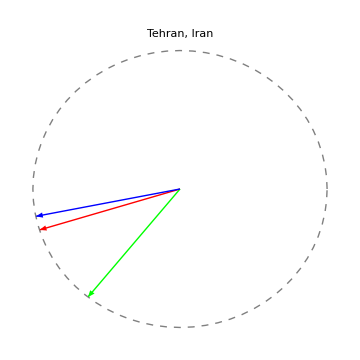

```mathematica
compareQibla[Tehran,Iran]
```

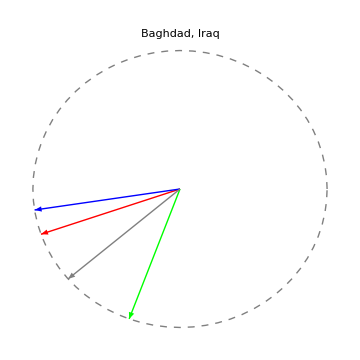

```mathematica
compareQibla[Baghdad,Iraq,229.5°]
```

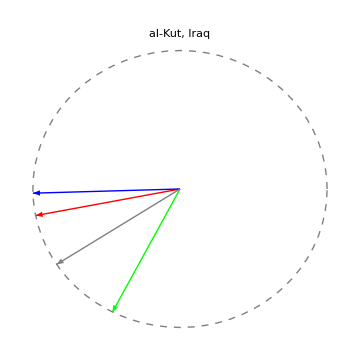

```mathematica
compareQibla["al-Kut",Iraq,237°]
```

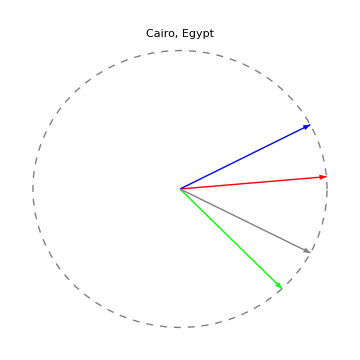

```mathematica
compareQibla[Cairo,Egypt,117.5°]
```

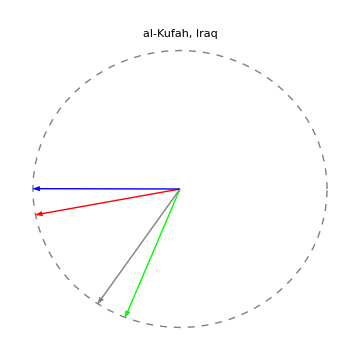

```mathematica
compareQibla["al-Kufah",Iraq,214°]
```